### Taylor Maclourin

```mathematica
FindTaylor[Func_,x0_,n_]:=Module[
{newFunc,CC,TaylorEqua,x,TaylorFunc},
newFunc[x_]:=Func[x+x0];
CC=Table[(D[newFunc[x],{x,ii}]/.x->0)/(ii!),{ii,0,n}];
TaylorEqua=Sum[CC[[ii+1]]*x^ii,{ii,0,n}];
TaylorFunc[u_]:=(TaylorEqua/.x->u-x0);
Return[{"CC"->CC,"Function"->TaylorFunc}];
]
```

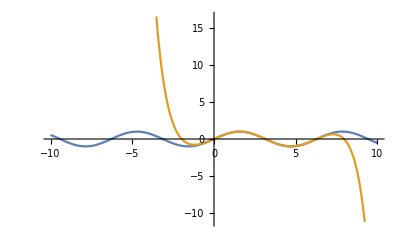

```mathematica
Func1[u_]:=Sin[u];
spFuncTaylor=FindTaylor[Func1,3,10];
Plot[{Sin[u],("Function"/.spFuncTaylor)[u]},{u,-10,10}]
```